# Razón de cambio: derivada

Ejercicio 1:
Representa en una misma ventana de graficación las funciones dadas y describe la relación entre ellas.
a) m(x)=3 √x
m1(x)=(g[x+0.01]-g[x])/0.01		b) n(x)=2x-x^2
n1(x)=(h[x+0.01]-h[x])/0.01

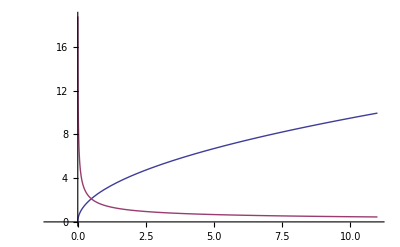

```mathematica
m[x_]:=3 √x
m1[x_]:=(m[x+0.01]-m[x])/0.01
n[x_]:=2x-x^2
n1[x_]:=(n[x+0.001]-n[x])/0.001
Plot[{m[x], m1[x]}, {x,-1,11}]
```

```mathematica
(*La linea azul es la grafica de la funcion y es creciente, mientras que la linea roja es la grafica de la funcion y va decreciendo(sin llegar a ser nunca negativa) ya que la pendiente de la linea azul es cada vez menor*)
```

```mathematica
Plot[{n[x],n1[x]}, {x,-4,6}]
```

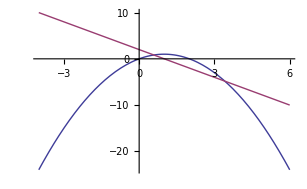
```mathematica
-Graphics-

(*La linea azul es la grafica de la funcion y es concava hacia abajo. La grafica de la derivada es la linea roja y tiene valores positivos hasta que llega al vertice (donde se hace cero) y tiene valores negativos cuando la funcion se hace decreciente*)+
```

Ejercicio 2:
Utilizar la gráfica y los puntos A(1,g(1)), B(1.5,g(1.5)), C(2,g(2)), D(2.5,g(2.5)) y E(3.5,g(3.5))  para responder a las siguientes preguntas
a) ¿Entre qué par de puntos es mayor la razón de cambio promedio de la función. 
b) ¿La razón de cambio promedio entre A y B es mayor o menor que la razón de cambio instantánea de B?
c) Trazar una recta tangente a la gráfica entre los puntos C y D cuya pendiente sea igual a la razón de cambio promedio de la función entre C y D.
d) Escribe un enunciado con la información del inciso c)

```mathematica
(*
a)Entre C y D
b)Es menor porque la tangente es igual a 3 y la recta secante entre A y B es 0.625.
*)
```

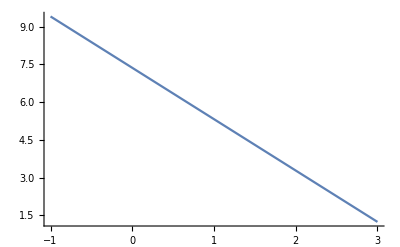

```mathematica
(*  c)   h[x] sera la funcion con pendiente de -2.04167       *)
h[x_]:=Expand[-2.04167(x-2.283785)+2.69948]

Plot[h[x],{x,-1,3}]
```

```mathematica
g'[x]
```

73/3-32 x+12 x^2-(4 x^3)/3

```mathematica
g'[2.283785]
```

```mathematica
-2.04167
```

```mathematica
g[2.283785]
```

2.69948

```mathematica
(*  
d) busque la derivada de la funcion g[x] y evalue el punto x=2.83785 que ya habia probado en la tabla para comprobar que la pendiente ahi fuera de -2.04167, luego evalue a la funcion g[x] en x=2.83785 y me dio y=2.69948... asi que la funcion de la recta con pendiente -2.04167, que pasa por el punto (2.83785,2.69948) es h[x]=-2.04167(x-2.283785)+2.69948
*)
```

```mathematica
g[x_]:=-1/3x(x-4)^3+3(x-4)+4;   (*Se define la función*)
xmin=0;
xmax=6;     (* se definen los extremos del dominio de la función*) 
ainicia=0;(* inicio del punto de tangencia*)
amin=0;
amax=6; (* se define el punto de tangencia mínimo y máximo*)
hinicia= 0;(*inicio del punto de intersección de la línea secante*)
hmin=0;
hmax=4.8;
Manipulate[
If[h==0,h=.001];
Grid[
{{Plot[{g[x],If[t1,g[a]+(D[g[t],t]/.t->a)*(x-a)],g[a]+((g[a+h]-g[a])/h)*(x-a)},{x,xmin,xmax},PlotStyle->{{Thickness[0.005],Black},{Thickness[0.004],Blue},{Thickness[0.004],Red}},PlotRange->{-5,6},ImageSize->{475,325},PlotLabel->Style[Row[{Style["g(x)",Italic],"=",
ToString[g[x],TraditionalForm]}],20],
AxesLabel->{Style["x",16,Italic],Style["y",16,Italic]},
Prolog->{{PointSize[0.02],If[t1,Blue,Red],Point[{a,f[a]}]},
   {PointSize[0.02],Red,Point[{a+h,g[a+h]}]}}]},
{Row[ 
{If[t1,Style[Text["Pendiente-tangente =" <> ToString[D[f[t],t]/.t->a]],Blue,20]],
Style[Text["Pendiente-secante =" <> ToString[(g[a+h]-f[a])/h]],Red,20]}, "   "]}}],
{{a,ainicia,"x0"},amin,amax},
{{h,hinicia,"h"},hmin,hmax},
{{t1,False,"Linea Tangente"},{True,False}},
TrackedSymbols->{a,h,t1},SaveDefinitions->True]
```

Ejercicio 3:
Calcular la derivada de las funciones dadas, usa el comando de derivada del software, después, en tu casa, calculas las derivadas a mano para verificar tu resultado (escaner la hoja de respuesta y subir como PDF)
b) Graficar en el mismo plano cartesiano a la función y a su derivada.
c) Describir el comportmiento de la función que corresponde a cualquier cero de la gráfica de la derivada. 
Nota: el comando para derivar es: f’[x]

```mathematica
f1[x_]:=(√x+1)/(x^2+1)
f2[x_]:=√((x+1)/x)
f3[x_]:=√((2x)/(x+1))
f4[x_]:=√(x-1)+√(x+1)
f5[x_]:=(Cos[Pi x]+1)/x
f6[x_]:=x^2 Tan[1/x]
```

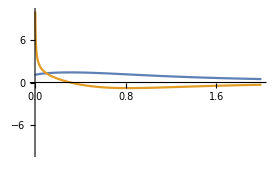
```mathematica
f1'[x]

-(2 (1+√x) x)/((1+x^2)^2)+1/(2 √x (1+x^2))

Plot[{f1[x],f1'[x]},{x,-2,2},PlotRange->{-10,10}]
-Graphics-
```

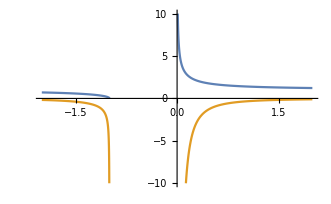
```mathematica
f2'[x]
(1/x-(1+x)/x^2)/(2 √((1+x)/x))
Plot[{f2[x],f2'[x]},{x,-2,2},PlotRange->{-10,10}]

-Graphics-
```

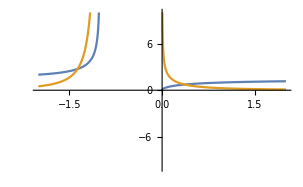
```mathematica
f3'[x]
(-x/(1+x)^2+1/(1+x))/(√2 √(x/(1+x)))
Plot[{f3[x],f3'[x]},{x,-2,2},PlotRange->{-10,10}]

-Graphics-
```

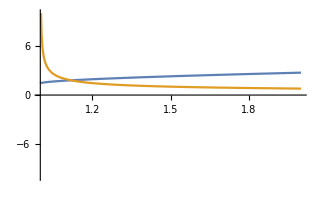
```mathematica
f4'[x]

1/(2 √(-1+x))+1/(2 √(1+x))

Plot[{f4[x],f4'[x]},{x,-2,2},PlotRange->{-10,10}]
-Graphics-
```

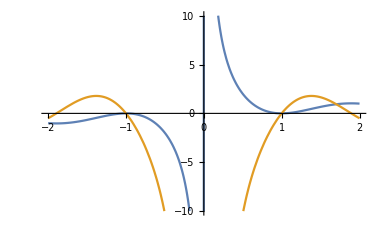
```mathematica
f5'[x]

-(1+Cos[π x])/x^2-(π Sin[π x])/x

Plot[{f5[x],f5'[x]},{x,-2,2},PlotRange->{-10,10}]
-Graphics-
```

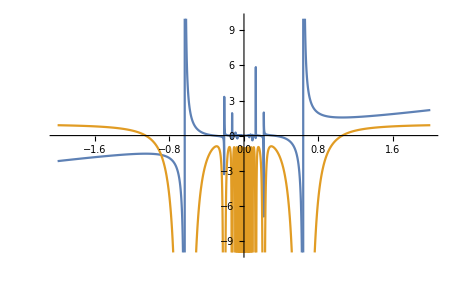
```mathematica
f6'[x]
-Sec[1/x]^2+2 x Tan[1/x]

Plot[{f6[x],f6'[x]},{x,-2,2},PlotRange->{-10,10}]
-Graphics-
```